```mathematica
Li6Li7basis = Flatten[Table[Table[{f1, m1, f2, m2},{m1, -f1,f1},{m2,-f2,f2}],{f1,1/2,3/2},{f2,1,2}],3]
```

{{1/2,-1/2,1,-1},{1/2,-1/2,1,0},{1/2,-1/2,1,1},{1/2,1/2,1,-1},{1/2,1/2,1,0},{1/2,1/2,1,1},{1/2,-1/2,2,-2},{1/2,-1/2,2,-1},{1/2,-1/2,2,0},{1/2,-1/2,2,1},{1/2,-1/2,2,2},{1/2,1/2,2,-2},{1/2,1/2,2,-1},{1/2,1/2,2,0},{1/2,1/2,2,1},{1/2,1/2,2,2},{3/2,-3/2,1,-1},{3/2,-3/2,1,0},{3/2,-3/2,1,1},{3/2,-1/2,1,-1},{3/2,-1/2,1,0},{3/2,-1/2,1,1},{3/2,1/2,1,-1},{3/2,1/2,1,0},{3/2,1/2,1,1},{3/2,3/2,1,-1},{3/2,3/2,1,0},{3/2,3/2,1,1},{3/2,-3/2,2,-2},{3/2,-3/2,2,-1},{3/2,-3/2,2,0},{3/2,-3/2,2,1},{3/2,-3/2,2,2},{3/2,-1/2,2,-2},{3/2,-1/2,2,-1},{3/2,-1/2,2,0},{3/2,-1/2,2,1},{3/2,-1/2,2,2},{3/2,1/2,2,-2},{3/2,1/2,2,-1},{3/2,1/2,2,0},{3/2,1/2,2,1},{3/2,1/2,2,2},{3/2,3/2,2,-2},{3/2,3/2,2,-1},{3/2,3/2,2,0},{3/2,3/2,2,1},{3/2,3/2,2,2}}

```mathematica
MFonehalf =Select[Li6Li7basis,#[[2]]+#[[4]]==1/2&]
```

{{1/2,-1/2,1,1},{1/2,1/2,1,0},{1/2,-1/2,2,1},{1/2,1/2,2,0},{3/2,-1/2,1,1},{3/2,1/2,1,0},{3/2,3/2,1,-1},{3/2,-3/2,2,2},{3/2,-1/2,2,1},{3/2,1/2,2,0},{3/2,3/2,2,-1}}

```mathematica
MFthreehalf =Select[Li6Li7basis,#[[2]]+#[[4]]==3/2&]
```

{{1/2,1/2,1,1},{1/2,-1/2,2,2},{1/2,1/2,2,1},{3/2,1/2,1,1},{3/2,3/2,1,0},{3/2,-1/2,2,2},{3/2,1/2,2,1},{3/2,3/2,2,0}}

```mathematica
MFfivehalf =Select[Li6Li7basis,#[[2]]+#[[4]]==5/2&]
```

{{1/2,1/2,2,2},{3/2,3/2,1,1},{3/2,1/2,2,2},{3/2,3/2,2,1}}

```mathematica
Li7s = 1/2;
Li7i = 3/2;
Li7gs = 2.0;
Li7gi = 2.170903;
Li6s = Li7s;
Li6i = 1;
Li6gs = Li7gs;
Li6gi = 0.822019;
```

```mathematica
ProjectionCoefficient[f1_,m1_,f2_,m2_,s_,ms_,i_,mi_,s1_,i1_,s2_,i2_]:= (-1)^(2i2-2s1-m1-m2-ms-mi)√((2f1+1)(2f2+1)(2s+1)(2i+1)) Sum[ThreeJSymbol[{s1,ms1},{i1,mi1},{f1, -m1}]*ThreeJSymbol[{s2,ms2},{i2,mi2},{f2,-m2}]*ThreeJSymbol[{s1,ms1},{s2,ms2},{s,-ms}]*ThreeJSymbol[{i1,mi1},{i2,mi2},{i,-mi}],{ms1,-s1,s1},{mi1,-i1,i1},{ms2,-s2,s2},{mi2,-i2,i2}];

ProjectionMatrixElement[f1_,m1_,f1p_,m1p_,f2_,m2_,f2p_,m2p_,s1_,i1_,s2_,i2_,S_]:= Sum[Sum[ProjectionCoefficient[f1,m1,f2,m2,s,ms,i,mi,s1,i1,s2,i2]*ProjectionCoefficient[f1p,m1p,f2p,m2p,s,ms,i,mi,s1,i1,s2,i2]*KroneckerDelta[s,S],{ms,-s,s},{mi,-i,i}],{s,Abs[s1-s2],Abs[s1+s2]},{i,Abs[i1-i2],Abs[i1+i2]}];
```

```mathematica
SingletProjectionMatrix= Table[Sum[Sum[ProjectionCoefficient[MFthreehalf[[j,1]],MFthreehalf[[j,2]],MFthreehalf[[j,3]],MFthreehalf[[j,4]],s,ms,i,mi,Li6s,Li6i,Li7s,Li7i]*ProjectionCoefficient[MFthreehalf[[jp,1]],MFthreehalf[[jp,2]],MFthreehalf[[jp,3]],MFthreehalf[[jp,4]],s,ms,i,mi,Li6s,Li6i,Li7s,Li7i] *KroneckerDelta[s,0],{ms,-s,s},{mi,-i,i}],{s,0,1},{i,Abs[Li6i-Li7i],Abs[Li6i+Li7i]}],{j,1,Length[MFthreehalf]},{jp,1,Length[MFthreehalf]}]
TripletProjectionMatrix = Table[Sum[Sum[ProjectionCoefficient[MFthreehalf[[j,1]],MFthreehalf[[j,2]],MFthreehalf[[j,3]],MFthreehalf[[j,4]],s,ms,i,mi,Li6s,Li6i,Li7s,Li7i]*ProjectionCoefficient[MFthreehalf[[jp,1]],MFthreehalf[[jp,2]],MFthreehalf[[jp,3]],MFthreehalf[[jp,4]],s,ms,i,mi,Li6s,Li6i,Li7s,Li7i]* KroneckerDelta[s,1],{ms,-s,s},{mi,-i,i}],{s,0,1},{i,Abs[Li6i-Li7i],Abs[Li6i+Li7i]}],{j,1,Length[MFthreehalf]},{jp,1,Length[MFthreehalf]}]
```

{{5/24,-1/(4 √3),1/(8 √3),1/(6 √2),-1/(4 √3),1/(2 √6),-1/(2 √6),1/(4 √3)},{-1/(4 √3),1/6,1/12,-(√(3/2))/10-1/(5 √6),0,-1/(5 √2)-(√2)/15,1/(6 √2),0},{1/(8 √3),1/12,7/24,-(√(3/2))/5+1/(10 √6),-1/4,1/(10 √2)-(2 √2)/15,-1/(6 √2),1/4},{1/(6 √2),-(√(3/2))/10-1/(5 √6),-(√(3/2))/5+1/(10 √6),7/24,(3 √(3/2))/20-1/(5 √6),1/(5 √3)+(√3)/10,-1/(5 √3)+(√3)/40,-(3 √(3/2))/20+1/(5 √6)},{-1/(4 √3),0,-1/4,(3 √(3/2))/20-1/(5 √6),1/4,0,1/(4 √2),-1/4},{1/(2 √6),-1/(5 √2)-(√2)/15,1/(10 √2)-(2 √2)/15,1/(5 √3)+(√3)/10,0,1/3,-1/6,0},{-1/(2 √6),1/(6 √2),-1/(6 √2),-1/(5 √3)+(√3)/40,1/(4 √2),-1/6,5/24,-1/(4 √2)},{1/(4 √3),0,1/4,-(3 √(3/2))/20+1/(5 √6),-1/4,0,-1/(4 √2),1/4}}

{{19/24,-1/(20 √3)+(√3)/10,1/(10 √3)-(3 √3)/40,-1/(6 √2),-1/(5 √3)+(3 √3)/20,-(√(2/3))/5-1/(10 √6),(√(3/2))/10+1/(5 √6),-1/(10 √3)-(√3)/20},{-1/(20 √3)+(√3)/10,5/6,-1/12,(4 √(2/3))/15+(√(3/2))/10-1/(3 √6),0,1/(5 √2)+(√2)/15,-3/(10 √2)+(√2)/15,0},{1/(10 √3)-(3 √3)/40,-1/12,17/24,(√(3/2))/10+1/(5 √6),1/4,3/(10 √2)-(√2)/15,1/(6 √2),-1/4},{-1/(6 √2),(4 √(2/3))/15+(√(3/2))/10-1/(3 √6),(√(3/2))/10+1/(5 √6),17/24,-(4 √(2/3))/15+(3 √(3/2))/20-1/(6 √6),-1/(2 √3),1/(5 √3)-(√3)/40,(2 √(2/3))/15+(√(3/2))/20-1/(6 √6)},{-1/(5 √3)+(3 √3)/20,0,1/4,-(4 √(2/3))/15+(3 √(3/2))/20-1/(6 √6),3/4,0,-7/(60 √2)-(√2)/15,1/4},{-(√(2/3))/5-1/(10 √6),1/(5 √2)+(√2)/15,3/(10 √2)-(√2)/15,-1/(2 √3),0,2/3,1/6,0},{(√(3/2))/10+1/(5 √6),-3/(10 √2)+(√2)/15,1/(6 √2),1/(5 √3)-(√3)/40,-7/(60 √2)-(√2)/15,1/6,19/24,23/(60 √2)-(√2)/15},{-1/(10 √3)-(√3)/20,0,-1/4,(2 √(2/3))/15+(√(3/2))/20-1/(6 √6),1/4,0,23/(60 √2)-(√2)/15,3/4}}

```mathematica
Li6Li7SingletProj={{5/24,-1/(4 √3),1/(8 √3),1/(6 √2),-1/(4 √3),1/(2 √6),-1/(2 √6),1/(4 √3)},{-1/(4 √3),1/6,1/12,-(√(3/2))/10-1/(5 √6),0,-1/(5 √2)-(√2)/15,1/(6 √2),0},{1/(8 √3),1/12,7/24,-(√(3/2))/5+1/(10 √6),-1/4,1/(10 √2)-(2 √2)/15,-1/(6 √2),1/4},{1/(6 √2),-(√(3/2))/10-1/(5 √6),-(√(3/2))/5+1/(10 √6),7/24,(3 √(3/2))/20-1/(5 √6),1/(5 √3)+(√3)/10,-1/(5 √3)+(√3)/40,-(3 √(3/2))/20+1/(5 √6)},{-1/(4 √3),0,-1/4,(3 √(3/2))/20-1/(5 √6),1/4,0,1/(4 √2),-1/4},{1/(2 √6),-1/(5 √2)-(√2)/15,1/(10 √2)-(2 √2)/15,1/(5 √3)+(√3)/10,0,1/3,-1/6,0},{-1/(2 √6),1/(6 √2),-1/(6 √2),-1/(5 √3)+(√3)/40,1/(4 √2),-1/6,5/24,-1/(4 √2)},{1/(4 √3),0,1/4,-(3 √(3/2))/20+1/(5 √6),-1/4,0,-1/(4 √2),1/4}};
```

```mathematica
Li6Li7TripletProj={{19/24,-1/(20 √3)+(√3)/10,1/(10 √3)-(3 √3)/40,-1/(6 √2),-1/(5 √3)+(3 √3)/20,-(√(2/3))/5-1/(10 √6),(√(3/2))/10+1/(5 √6),-1/(10 √3)-(√3)/20},{-1/(20 √3)+(√3)/10,5/6,-1/12,(4 √(2/3))/15+(√(3/2))/10-1/(3 √6),0,1/(5 √2)+(√2)/15,-3/(10 √2)+(√2)/15,0},{1/(10 √3)-(3 √3)/40,-1/12,17/24,(√(3/2))/10+1/(5 √6),1/4,3/(10 √2)-(√2)/15,1/(6 √2),-1/4},{-1/(6 √2),(4 √(2/3))/15+(√(3/2))/10-1/(3 √6),(√(3/2))/10+1/(5 √6),17/24,-(4 √(2/3))/15+(3 √(3/2))/20-1/(6 √6),-1/(2 √3),1/(5 √3)-(√3)/40,(2 √(2/3))/15+(√(3/2))/20-1/(6 √6)},{-1/(5 √3)+(3 √3)/20,0,1/4,-(4 √(2/3))/15+(3 √(3/2))/20-1/(6 √6),3/4,0,-7/(60 √2)-(√2)/15,1/4},{-(√(2/3))/5-1/(10 √6),1/(5 √2)+(√2)/15,3/(10 √2)-(√2)/15,-1/(2 √3),0,2/3,1/6,0},{(√(3/2))/10+1/(5 √6),-3/(10 √2)+(√2)/15,1/(6 √2),1/(5 √3)-(√3)/40,-7/(60 √2)-(√2)/15,1/6,19/24,23/(60 √2)-(√2)/15},{-1/(10 √3)-(√3)/20,0,-1/4,(2 √(2/3))/15+(√(3/2))/20-1/(6 √6),1/4,0,23/(60 √2)-(√2)/15,3/4}};
```

```mathematica
N[MatrixForm[Li6Li7SingletProj.Li6Li7SingletProj-Li6Li7SingletProj]]
```

(0. | 3.46945×10^-18 | 3.46945×10^-18 | 4.16334×10^-17 | -6.93889×10^-18 | -1.38778×10^-17 | -1.73472×10^-18 | 6.93889×10^-18
3.46945×10^-18 | -6.93889×10^-18 | -6.93889×10^-18 | 2.77556×10^-17 | 6.93889×10^-18 | -2.77556×10^-17 | 1.73472×10^-18 | -6.93889×10^-18
3.46945×10^-18 | -6.93889×10^-18 | -6.93889×10^-18 | 0. | 1.04083×10^-17 | 1.38778×10^-17 | 3.46945×10^-18 | -1.04083×10^-17
4.16334×10^-17 | 2.77556×10^-17 | 0. | 0. | 0. | 0. | -2.77556×10^-17 | 0.
-6.93889×10^-18 | 6.93889×10^-18 | 1.04083×10^-17 | 0. | -8.67362×10^-18 | 0. | 0. | 8.67362×10^-18
-1.38778×10^-17 | -2.77556×10^-17 | 1.38778×10^-17 | 0. | 0. | 0. | -6.93889×10^-18 | 0.
-1.73472×10^-18 | 1.73472×10^-18 | 3.46945×10^-18 | -2.77556×10^-17 | 0. | -6.93889×10^-18 | 3.46945×10^-18 | 0.
6.93889×10^-18 | -6.93889×10^-18 | -1.04083×10^-17 | 0. | 8.67362×10^-18 | 0. | 0. | -8.67362×10^-18)

```mathematica
N[MatrixForm[Li6Li7TripletProj.Li6Li7TripletProj-Li6Li7TripletProj]]
```

(1.38778×10^-17 | 0. | 1.38778×10^-17 | 3.46945×10^-17 | -2.77556×10^-17 | 0. | -5.55112×10^-17 | -4.85723×10^-17
0. | -1.38778×10^-17 | 0. | 0. | -2.42861×10^-17 | 0. | 1.38778×10^-17 | 3.46945×10^-18
1.38778×10^-17 | 0. | -1.38778×10^-17 | 2.77556×10^-17 | 1.04083×10^-17 | -2.77556×10^-17 | 6.93889×10^-18 | -1.38778×10^-17
3.46945×10^-17 | 0. | 2.77556×10^-17 | 6.93889×10^-18 | 0. | 6.93889×10^-18 | 1.73472×10^-17 | 0.
-2.77556×10^-17 | -2.42861×10^-17 | 1.04083×10^-17 | 0. | -2.08167×10^-17 | 1.73472×10^-17 | -5.55112×10^-17 | 1.38778×10^-17
0. | 0. | -2.77556×10^-17 | 6.93889×10^-18 | 1.73472×10^-17 | 1.38778×10^-17 | -1.38778×10^-17 | 6.93889×10^-18
-5.55112×10^-17 | 1.38778×10^-17 | 6.93889×10^-18 | 1.73472×10^-17 | -5.55112×10^-17 | -1.38778×10^-17 | -2.08167×10^-17 | 5.55112×10^-17
-4.85723×10^-17 | 3.46945×10^-18 | -1.38778×10^-17 | 0. | 1.38778×10^-17 | 6.93889×10^-18 | 5.55112×10^-17 | 0.)

```mathematica
invcminHartree = 4.5563352812122295*10^-6;
AngstrominBohr = 1/0.529177210903;
Li7A = 401.75204335 * 10^-6;
Li6A = 152.0*10^-6;
Li7Acm = (Li7A *6.626*10^-34*10^12)/(1.986*10^-23);
Li6Acm = (Li6A *6.626*10^-34*10^12)/(1.986*10^-23);
Li7AH = Li7Acm*invcminHartree;
Li6AH = Li6Acm*invcminHartree;
μb = (9.27*10^-24)/(6.626*10^-34)*10^-12*(1/10^4);
μn = (5.0507837461*10^-27)/(6.626*10^-34)*10^-12*(1/10^4);
μbcm = (μb *6.626*10^-34*10^12)/(1.986*10^-23);
μncm = (μn *6.626*10^-34*10^12)/(1.986*10^-23);
μbH=μbcm*invcminHartree;
μnH=μncm*invcminHartree;
```

```mathematica
HZ[f_,m_,fp_,mp_,s_,i_,gs_,gi_,A_,B_,μb_,μn_]:= A/2(f(f+1)-i(i+1)-s(s+1))KroneckerDelta[f,fp] KroneckerDelta[m,mp]+gs μb B Sqrt[(2fp+1)(2f+1)]Sum[ms ThreeJSymbol[{s, ms},{i, mi},{fp, -mp}]ThreeJSymbol[{s, ms},{i, mi},{f, -m}],{ms, -s,s},{mi,-i,i}]KroneckerDelta[m,mp]+gi μn B Sqrt[(2fp+1)(2f+1)]Sum[mi ThreeJSymbol[{s, ms},{i, mi},{fp, -mp}]ThreeJSymbol[{s, ms},{i, mi},{f, -m}],{ms, -s,s},{mi,-i,i}]KroneckerDelta[m,mp];
```

```mathematica
Li6Li7HZ[B_]=FullSimplify[Table[HZ[MFthreehalf[[j,1]],MFthreehalf[[j,2]],MFthreehalf[[jp,1]],MFthreehalf[[jp,2]],Li6s,Li6i, Li6gs,Li6gi,Li6AH,B,μbH,μnH]+HZ[MFthreehalf[[j,3]],MFthreehalf[[j,4]],MFthreehalf[[jp,3]],MFthreehalf[[jp,4]],Li6s,Li6i, Li6gs,Li6gi,Li6AH,B,μbH,μnH],{j,1,Length[MFthreehalf]},{jp,1,Length[MFthreehalf]}]];
```

```mathematica
MatrixForm[Li6Li7HZ[0]]
```

(-3.17712×10^-8 | 0. | -2.31064×10^-8 | -8.66488×10^-9 | 0. | 0. | 0. | 0.
0. | 1.44415×10^-8 | 0. | 0. | 0. | 3.75478×10^-8 | 0. | 0.
-2.31064×10^-8 | 0. | 1.44415×10^-8 | 0. | 0. | 0. | 3.75478×10^-8 | 0.
-8.66488×10^-9 | 0. | 0. | 2.88829×10^-9 | 0. | 0. | 1.15532×10^-8 | 0.
0. | 0. | 0. | 0. | 2.88829×10^-9 | 0. | 0. | 1.15532×10^-8
0. | 3.75478×10^-8 | 0. | 0. | 0. | 4.9101×10^-8 | 0. | 0.
0. | 0. | 3.75478×10^-8 | 1.15532×10^-8 | 0. | 0. | 4.9101×10^-8 | 0.
0. | 0. | 0. | 0. | 1.15532×10^-8 | 0. | 0. | 4.9101×10^-8)

### ^6 Li +^7 Li Potential Energy Curves

```mathematica
SingletDe = 8516.709;
Singletre = 2.6729932;
Singletref = 3.85;
SingletC6 = 6.71527 * 10^6;
SingletC8 = 1.12588 * 10^8;
SingletC10 = 2.78604 * 10^9;
p = 5;
q = 3;
Singletβcf = {-2.89828701, -1.309265,-2.018507, -1.38162,-1.21933, 0.3463, 0.1061,-0.1886,1.671,10.943,3.944,-27.23,-11.49,56.7, 38.9,-37.4, -33.0};
SingletUcf = {0.19400, -0.0100, 0.390};
SingletUinf = 0;
pad = 6;
qad = pad; 
TripletDe = 333.758;
Tripletre = 4.17005000;
Tripletref=8.0;
TripletC6 = 6.7185*10^6;
TripletC8 =1.12629*10^8;
TripletC10 = 2.78683*10^9;
Tripletβcf =  {-0.51608,-0.09782, 0.1137, -0.0248};
TripletUcf = {0.059};
TripletUinf = SingletUinf;
ρ = 0.54;
y[rp_,r_,p_]:=(r^p-rp^p)/(r^p+rp^p);
βfun[r_,βcf_,βinf_,ypeq_,ypref_,yqref_]:= βinf ypref+(1-ypref)* Sum[βcf[[j+1]]*(yqref)^j,{j,0,Length[βcf]-1}];
Singletulr[r_,c6_,c8_,c10_]:= c6/r^6+c8/r^8+c10/r^10;
Singletβinf=Log[(2 SingletDe)/Singletulr[Singletre,SingletC6,SingletC8,SingletC10]];
SingletVMLR[r_]:= SingletDe(1-Singletulr[r,SingletC6,SingletC8,SingletC10]/Singletulr[Singletre,SingletC6,SingletC8,SingletC10]*Exp[-βfun[r,Singletβcf,Singletβinf,y[Singletre,r,q],y[Singletref,r,p],y[Singletref,r,q]]*y[Singletre,r,p]])^2-SingletDe;
DDS[r_,m_,bds_,cds_,ρ_,s_]:= (1-Exp[-(ρ r)(bds/m+(cds (ρ r))/m^(1/2))])^(m+s);
DDSTriplet[m_,r_]:= DDS[r,m,3.30,0.423,ρ,-1];
Tripletulr[r_]:= DDSTriplet[6,r] TripletC6/r^6+DDSTriplet[8,r] TripletC8/r^8+DDSTriplet[10,r] TripletC10/r^10;
Tripletβinf=Log[(2 TripletDe)/Tripletulr[Tripletre]];
βTriplet[r_]:= Tripletβinf*y[Tripletref,r,5]+(1-y[Tripletref,r,5])*Sum[Tripletβcf[[j+1]]*y[Tripletref,r,3]^j,{j,0,Length[Tripletβcf]-1}];
TripletVMLR[r_]:= TripletDe(1-Tripletulr[r]/Tripletulr[Tripletre]*Exp[-βTriplet[r]*y[Tripletre,r,p]])^2-TripletDe;
```

```mathematica
amu = 1822.89;
massLi7 = 7.016004*amu;
massLi6 = 6.0151227950*amu;
Δm = massLi6-massLi7;
massfactor = Δm/massLi6;
```

```mathematica
SingletΔDe = massfactor(SingletUinf-SingletUcf[[1]])
TripletΔDe = massfactor (TripletUinf-TripletUcf[[1]])
```

0.0322805

0.00981725

```mathematica
Singlet67De = SingletDe+SingletΔDe
Triplet67De = TripletDe+TripletΔDe
```

8516.74

333.768

```mathematica
Series[SingletVMLR[r],{r,Singletre,2}]
Series[TripletVMLR[r],{r,Tripletre,2}]
```

-8516.71-3.28496×10^-12 (r-2.67299)+6424.64 (r-2.67299)^2+O[r-2.67299]^3

-333.758-1.21067×10^-13 (r-4.17005)+222.679 (r-4.17005)^2+O[r-4.17005]^3

```mathematica
Singletkbar=6424.64*2;
Tripletkbar=222.679*2;
```

```mathematica
Stildeprime[ucf0_,ucf1_,uinf_,pad_,qad_,re_]:= ((uinf-ucf0)pad + ucf1 qad)/(2 re);
SingletΔre = -massfactor (1/Singletkbar Stildeprime[SingletUcf[[1]],SingletUcf[[2]],SingletUinf,pad,qad,Singletre])
TripletΔre = -massfactor (Stildeprime[TripletUcf[[1]],0,TripletUinf,pad,qad,Tripletre]/Tripletkbar)
```

-2.96492×10^-6

-0.0000158585

```mathematica
Singlet67re = Singletre + SingletΔre
Triplet67re = Tripletre+TripletΔre
```

2.67299

4.17003

```mathematica
Stilde[r_,pad_,uinf_,ucf_,qad_,re_]:= y[re,r,pad] uinf +(1-y[re,r,pad]) Sum[ucf[[i+1]] y[re,r,qad]^i,{i,0,Length[ucf]-1}];
TripletΔVad[r_]:= massfactor*Stilde[r,pad,TripletUinf,TripletUcf,qad,Tripletre];
SingletΔVad[r_]:= massfactor*Stilde[r,pad,SingletUinf,SingletUcf,qad,Singletre];
```

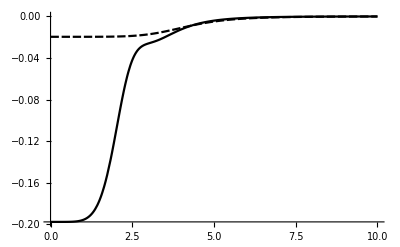

```mathematica
Plot[{SingletΔVad[r],TripletΔVad[r]},{r,0,10},PlotRange->Full]
```

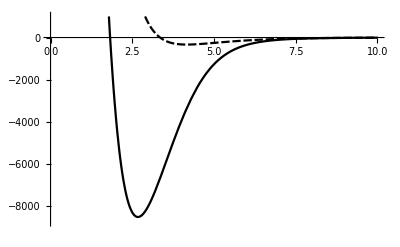

```mathematica
Triplet67VMLR[r_]:= TripletVMLR[r]+TripletΔVad[r];
Singlet67VMLR[r_]:= SingletVMLR[r]+SingletΔVad[r];
Plot[{Singlet67VMLR[r],Triplet67VMLR[r]},{r,1.0,10},PlotRange->{-8750,1000}]
```

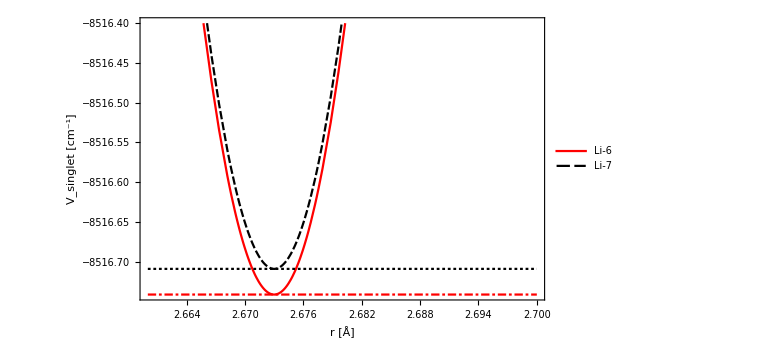

```mathematica
Plot[{Singlet67VMLR[r],SingletVMLR[r],-SingletDe,-Singlet67De},{r,2.660,2.70},PlotRange->{-8516.4,-8516.8},Frame->True,Frame->True,FrameLabel->{"r [Å]", "V_singlet [cm^-1]"},ImageSize->Large,PlotLegends->{"Li-6","Li-7"},LabelStyle->Large,PlotStyle->{Red,Black,Black,Red}]
```

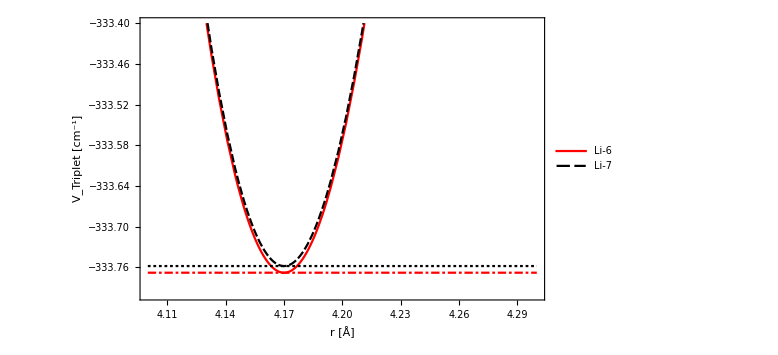

```mathematica
Plot[{Triplet67VMLR[r],TripletVMLR[r],-TripletDe,-Triplet67De},{r,4.1,4.3},PlotRange->{-333.8,-333.4},Frame->True,Frame->True,FrameLabel->{"r [Å]", "V_Triplet [cm^-1]"},ImageSize->Large,PlotStyle->{Red,Black,Black,Red},PlotLegends->{"Li-6","Li-7"},LabelStyle->Large]
```

### Conversion to Atomic Units

```mathematica
Rmax=400;
Rmin=0.005;
NR =10000;
dR=(Rmax-Rmin)/NR;
RGrid =Table[Rmin+dR i,{i,1,NR}];
XLi67MLRdat = Table[{RGrid[[i]],Singlet67VMLR[RGrid[[i]]]},{i,1,NR}];
XLi67MLRHBdat = Table[{RGrid[[i]]*AngstrominBohr, XLi67MLRdat[[i,2]]*invcminHartree},{i,1,Length[XLi67MLRdat]}];
XLi67MLRHB = Interpolation[XLi67MLRHBdat]
```

InterpolatingFunction[…]

```mathematica
ALi67MLRdat = Table[{RGrid[[i]],Triplet67VMLR[RGrid[[i]]]},{i,1,NR}];
ALi67MLRHBdat = Table[{RGrid[[i]]*AngstrominBohr, ALi67MLRdat[[i,2]]*invcminHartree},{i,1,Length[ALi67MLRdat]}];
ALi67MLRHB = Interpolation[ALi67MLRHBdat]
```

InterpolatingFunction[…]

### Hyperfine and Zeeman Structure of Potentials

```mathematica
HLi67total[r_,B_]= Li6Li7HZ[B]+Li6Li7TripletProj*ALi67MLRHB[r]+Li6Li7SingletProj*XLi67MLRHB[r];
```

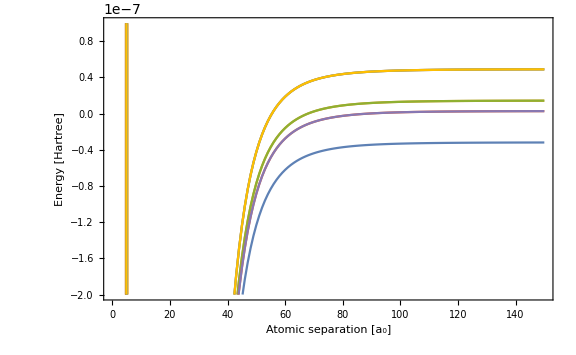

```mathematica
phf =ListLinePlot[{Table[{j, HLi67total[j, 0][[1, 1]]}, {j, 2, 150}], Table[{j, HLi67total[j, 0][[2, 2]]}, {j, 2, 150}], Table[{j, HLi67total[j, 0][[3, 3]]}, {j, 2, 150}], Table[{j, HLi67total[j, 0][[4, 4]]}, {j, 2, 150}], Table[{j, HLi67total[j, 0][[5, 5]]}, {j, 2, 150}], Table[{j, HLi67total[j, 0][[6, 6]]}, {j, 2, 150}], Table[{j, HLi67total[j, 0][[7, 7]]}, {j, 2, 150}], Table[{j, HLi67total[j, 0][[8, 8]]}, {j, 2, 150}]},Frame->True,ImageSize->Large,FrameLabel->{"Atomic separation [a_0]","Energy [Hartree]"},LabelStyle->Large,PlotRange->{-2*10^-7,1*10^-7}]
```

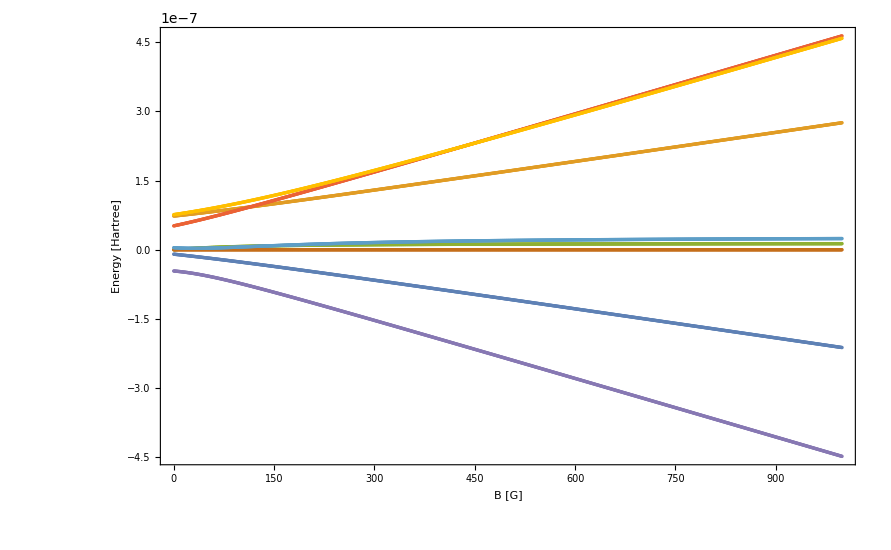

```mathematica
EigenTable[B_]= Sort[Eigenvalues[Li6Li7HZ[B]]];
Test1 = Table[{j,EigenTable[j][[1]]},{j,0,1000}];
Test2 = Table[{j,EigenTable[j][[2]]},{j,0,1000}];
Test3 = Table[{j,EigenTable[j][[3]]},{j,0,1000}];
Test4 = Table[{j,EigenTable[j][[4]]},{j,0,1000}];
Test5 = Table[{j,EigenTable[j][[5]]},{j,0,1000}];
Test6 = Table[{j,EigenTable[j][[6]]},{j,0,1000}];
Test7 = Table[{j,EigenTable[j][[7]]},{j,0,1000}];
Test8 = Table[{j,EigenTable[j][[8]]},{j,0,1000}];
phz =ListPlot[{Test1[[1;;1000]],Test2[[1;;1000]],Test3[[1;;1000]],Test4[[1;;1000]],Test5[[1;;1000]],Test6[[1;;1000]],Test7[[1;;1000]],Test8[[1;;1000]]},ImageSize->Large,Frame->True,FrameLabel->{"B [G]","Energy [Hartree]"},LabelStyle->Large]
```

### Calculation of scattering lengths for the singlet and triplet potentials

```mathematica
Li6Li7μ = (massLi7*massLi6)/(massLi7+massLi6)
```

5903.54

```mathematica
CalcCotanDeltaTriplet[Εtest_,rmax_,rmin_,μ_]:=
Module[{CotanDelta,sol,k,u1,u2,r1,r2,u},
r1=0.95 rmax;
r2=0.99rmax;
k=√(2 μ Εtest);
sol=NDSolve[{-1/(2 μ)u''[r]+ALi67MLRHB[r] u[r]==Εtest u[r],u[rmin]==0,u'[rmin]==10^-10},u,{r,rmin,rmax}];
u1=u[r1]/.sol[[1]];
u2=u[r2]/.sol[[1]];
CotanDelta=(-u2 Cos[k r1]+u1 Cos[k r2])/(u2 Sin[k r1]-u1 Sin[k r2]);
Return[CotanDelta]
]

CalcERETriplet[rmax_,rmin_,ΕMin_,ΕMax_,μ_]:=
Module[{EREData,ascat,reff,A,B,fitpars,dE},
dE=(ΕMax-ΕMin)/10;
EREData=Table[{2μ Εtest,√(2μ Εtest)CalcCotanDeltaTriplet[Εtest,rmax,rmin,μ]},{Εtest,ΕMin,ΕMax,dE}];
fitpars=FindFit[EREData,A+B ksqr,{A,B},ksqr];
ascat=-1/A/.fitpars;
reff=2B/.fitpars;
Return[{ascat,reff,EREData}]
]
{Tripletascat,Tripletreff,TripletEREData}=CalcERETriplet[500,2,10^-10,5*10^-9,Li6Li7μ]
```

{40.7753,38.9201,{{1.18071×10^-6,-0.0245193},{6.96618×10^-6,-0.024395},{0.0000127517,-0.0242741},{0.0000185371,-0.0241563},{0.0000243226,-0.0240411},{0.0000301081,-0.0239282},{0.0000358935,-0.0238174},{0.000041679,-0.0237084},{0.0000474645,-0.023601},{0.00005325,-0.023495},{0.0000590354,-0.0233903}}}

```mathematica
CalcCotanDeltaSinglet[Εtest_,rmax_,rmin_,μ_]:=
Module[{CotanDelta,sol,k,u1,u2,r1,r2,u},
r1=0.95 rmax;
r2=0.99rmax;
k=√(2 μ Εtest);
sol=NDSolve[{-1/(2 μ)u''[r]+XLi67MLRHB[r] u[r]==Εtest u[r],u[rmin]==0,u'[rmin]==10^-10},u,{r,rmin,rmax}];
u1=u[r1]/.sol[[1]];
u2=u[r2]/.sol[[1]];
CotanDelta=(-u2 Cos[k r1]+u1 Cos[k r2])/(u2 Sin[k r1]-u1 Sin[k r2]);
Return[CotanDelta]
]

CalcERESinglet[rmax_,rmin_,ΕMin_,ΕMax_,μ_]:=
Module[{EREData,ascat,reff,A,B,fitpars,dE},
dE=(ΕMax-ΕMin)/10;
EREData=Table[{2μ Εtest,√(2μ Εtest)CalcCotanDeltaSinglet[Εtest,rmax,rmin,μ]},{Εtest,ΕMin,ΕMax,dE}];
fitpars=FindFit[EREData,A+B ksqr,{A,B},ksqr];
ascat=-1/A/.fitpars;
reff=2B/.fitpars;
Return[{ascat,reff,EREData}]
]
{Singletascat,Singletreff,SingletEREData}=CalcERESinglet[500,2,10^-10,5*10^-9,Li6Li7μ]
```

{-17.4359,1075.14,{{1.18071×10^-6,0.0588571},{6.96618×10^-6,0.061481},{0.0000127517,0.0641906},{0.0000185371,0.0669942},{0.0000243226,0.0699006},{0.0000301081,0.0729196},{0.0000358935,0.0760612},{0.000041679,0.0793362},{0.0000474645,0.0827569},{0.00005325,0.0863358},{0.0000590354,0.0900868}}}

### Wavefunctions for Singlet and Triplet Potentials

```mathematica
Εtest = 10^-16;
solsg = NDSolveValue[{-1/(2 Li6Li7μ)u''[r]+XLi67MLRHB[r] u[r]==Εtest u[r],u[2.0]==0,u'[2.0]==10^-10},u,{r,2.0,500}]
soltp = NDSolveValue[{-1/(2 Li6Li7μ)u''[r]+ALi67MLRHB[r] u[r]==Εtest u[r],u[2.0]==0,u'[2.0]==10^-10},u,{r,2.0,500}]
```

InterpolatingFunction[…]

InterpolatingFunction[…]

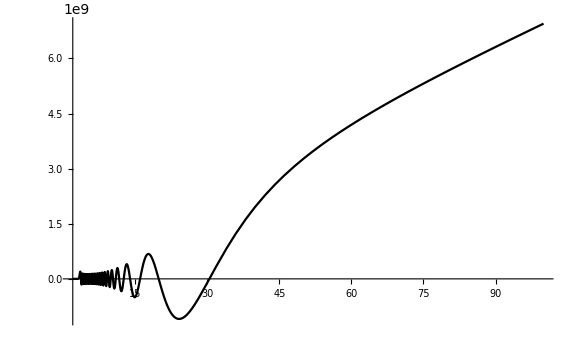

```mathematica
Plot[{solsg[r]},{r,2,100},ImageSize->Large,LabelStyle->Large]
```

```mathematica
Plot[{soltp[r]},{r,2,100},ImageSize->Large,LabelStyle->Large]
```

-Graphics-